```mathematica
ClearAll["Global`*"]
```

```mathematica
ass={x>0};
```

```mathematica
n=100
```

100

```mathematica
X[x_]:={Sin[2 π x],x}
```

```mathematica
ν[x_]:=FullSimplify[Norm[X'[x]],Assumptions->ass]
```

```mathematica
ψ[x_]:=FullSimplify[ArcTan[X'[x][[1]],-X'[x][[2]]],Assumptions->ass]
```

```mathematica
v[x_]:=1
```

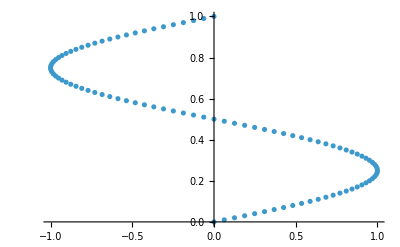

```mathematica
ListPlot[Table[X[i/n],{i,0,n}]]
```

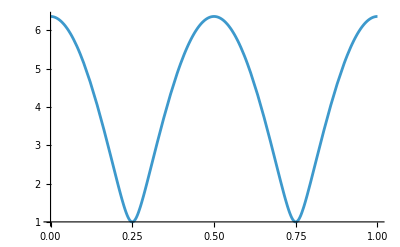

```mathematica
Plot[v[x]ν[x],{x,0,1}]
```

```mathematica
(*write X*)
```

```mathematica
t=Table[{X[i/n][[1]], X[i/n][[2]],0,i/n,0,0},{i,0,n}]//N
```

```mathematica
PrependTo[t,{"f:0","f:1","f:2",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/work/manuscripts/paper_ale/figures/figure_4/solution/snapshots/csv/nodal_values/X_n_12_1.csv",t];
```

```mathematica
(*write ν*)
```

```mathematica
t=Table[{ν[i/n],0,i/n,0,0},{i,0,n}]//N
```

```mathematica
PrependTo[t,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/work/manuscripts/paper_ale/figures/figure_4/solution/snapshots/csv/nodal_values/nu_n_12_1.csv",t];
```

```mathematica
(*write ψ*)
```

```mathematica
t=Table[{ψ[i/n],0,i/n,0,0},{i,0,n}]//N
```

```mathematica
PrependTo[t,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/work/manuscripts/paper_ale/figures/figure_4/solution/snapshots/csv/nodal_values/psi_n_12_1.csv",t];
```

```mathematica
(*write v*)
```

```mathematica
t=Table[{v[i/n],0,0,i/n,0,0},{i,0,n}]//N
```

```mathematica
PrependTo[t,{"f:0","f:1","f:2",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/work/manuscripts/paper_ale/figures/figure_4/solution/snapshots/csv/nodal_values/v_n_1.csv",t];
```